#### Dicke Picture

```mathematica
n=5;
Δ=Table[ConstantArray[0,{Binomial[n,i],Binomial[n,i]}],{i,0,n}];
Table[Δ[[i+1]]//MatrixForm,{i,0,n}]
f[n_Integer,l__]:=Module[
{},
ReplacePart[ConstantArray[0,n],Table[#[[i]]->1,{i,Length@#}]]&/@l
]
f[n,#]&/@Table[Subsets[Range[n],{i}],{i,0,n}];
couple[n_,np_]:=Module[
{states,couplings},
states=f[n,#]&/@Table[Subsets[Range[n],{i}],{i,np-1,np}];
couplings=Table[If[
Total[If[#[[1]]==#[[2]],0,1]&/@Transpose@{states[[1,i]],states[[2,j]]}]==1,
1,0],{i,Length@states[[1]]},{j,Length@states[[2]]}];
Return[couplings];
]
as=Table[couple[n,i],{i,n}]/2;
Table[as[[i]]//MatrixForm,{i,n}]
```

{(0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0),(0)}

{(1/2 | 1/2 | 1/2 | 1/2 | 1/2),(1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 1/2),(1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2),(1/2 | 1/2 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0
1/2 | 0 | 0 | 1/2 | 0
0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 0 | 1/2
0 | 1/2 | 0 | 0 | 1/2
0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 1/2 | 1/2),(1/2
1/2
1/2
1/2
1/2)}

```mathematica
H=ArrayFlatten@{
{Δ[[1]],as[[1]],0,0,0,0},
{Transpose[as[[1]]],Δ[[2]],as[[2]],0,0,0},
{0,Transpose[as[[2]]],Δ[[3]],as[[3]],0,0},
{0,0,Transpose[as[[3]]],Δ[[4]],as[[4]],0},
{0,0,0,Transpose[as[[4]]],Δ[[5]],as[[5]]},
{0,0,0,0,Transpose[as[[5]]],Δ[[6]]}
};
MatrixForm@H
```

(0 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 0)

```mathematica
Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}]
Hb=ArrayFlatten@{
{Δb[[1]],as[[1]],0,0,0,0},
{Transpose[as[[1]]],Δb[[2]],as[[2]],0,0,0},
{0,Transpose[as[[2]]],Δb[[3]],as[[3]],0,0},
{0,0,Transpose[as[[3]]],Δb[[4]],as[[4]],0},
{0,0,0,Transpose[as[[4]]],Δb[[5]],as[[5]]},
{0,0,0,0,Transpose[as[[5]]],Δb[[6]]}
};
MatrixForm@Hb
```

{{{0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{40,0,0,0,0,0,0,0,0,0},{0,40,0,0,0,0,0,0,0,0},{0,0,40,0,0,0,0,0,0,0},{0,0,0,40,0,0,0,0,0,0},{0,0,0,0,40,0,0,0,0,0},{0,0,0,0,0,40,0,0,0,0},{0,0,0,0,0,0,40,0,0,0},{0,0,0,0,0,0,0,40,0,0},{0,0,0,0,0,0,0,0,40,0},{0,0,0,0,0,0,0,0,0,40}},{{120,0,0,0,0,0,0,0,0,0},{0,120,0,0,0,0,0,0,0,0},{0,0,120,0,0,0,0,0,0,0},{0,0,0,120,0,0,0,0,0,0},{0,0,0,0,120,0,0,0,0,0},{0,0,0,0,0,120,0,0,0,0},{0,0,0,0,0,0,120,0,0,0},{0,0,0,0,0,0,0,120,0,0},{0,0,0,0,0,0,0,0,120,0},{0,0,0,0,0,0,0,0,0,120}},{{240,0,0,0,0},{0,240,0,0,0},{0,0,240,0,0},{0,0,0,240,0},{0,0,0,0,240}},{{400}}}

(0 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 120 | 0 | 0 | 0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 240 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 240 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 240 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 240 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 240 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 400)

```mathematica
U[t_,H__]:=MatrixExp[-ⅈ 2π H t]
```

```mathematica
$PlotTheme="Detailed"
```

Detailed

```mathematica
psi0=UnitVector[Length@H,1];(* ground *)
```

```mathematica
ts=Range[0,1.5,0.001];

psi0=(UnitVector[Length@H,2]-UnitVector[Length@H,3])/√2;(* non-W, singley excited *)
psis=U[#,H].psi0&/@ts;
gsnonW=Transpose@{ts,Abs[UnitVector[Length@H,1].#]^2&/@psis};
onesnonW=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psis};
twos=Transpose@{ts,Total[Abs[#[[2+n;;3n+1]]]^2]&/@psis};
threes=Transpose@{ts,Total[Abs[#[[3n+2;;5n+1]]]^2]&/@psis};
fours=Transpose@{ts,Total[Abs[#[[5n+2;;6n+1]]]^2]&/@psis};
fives=Transpose@{ts,Total[Abs[#[[-1;;-1]]]^2]&/@psis};
gte2nonW=Transpose@{ts,Total[Abs[#[[2+n;;-1]]]^2]&/@psis};

psi0=Sum[UnitVector[Length@H,i+1],{i,n}]/√n;(* W *)
psis=U[#,H].psi0&/@ts;
gsW=Transpose@{ts,Abs[UnitVector[Length@H,1].#]^2&/@psis};
onesW=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psis};
gte2W=Transpose@{ts,Total[Abs[#[[2+n;;-1]]]^2]&/@psis};

psi0=UnitVector[Length@H,1];(* ground *)
psis=U[#,H].psi0&/@ts;
gsg=Transpose@{ts,Abs[UnitVector[Length@H,1].#]^2&/@psis};
onesg=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psis};
gte2g=Transpose@{ts,Total[Abs[#[[2+n;;-1]]]^2]&/@psis};
```

```mathematica
tsb=Range[0,1.5,0.001];
psisb=U[#,Hb].UnitVector[Length@Hb,1]&/@tsb;
gsb=Transpose@{ts,Abs[UnitVector[Length@Hb,1].#]^2&/@psisb};
onesb=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};
twosb=Transpose@{ts,Total[Abs[#[[2+n;;3n+1]]]^2]&/@psisb};
threesb=Transpose@{ts,Total[Abs[#[[3n+2;;5n+1]]]^2]&/@psisb};
foursb=Transpose@{ts,Total[Abs[#[[5n+2;;6n+1]]]^2]&/@psisb};
fivesb=Transpose@{ts,Total[Abs[#[[-1;;-1]]]^2]&/@psisb};
```

```mathematica
ll=LineLegend[{"|0ψ(t)|^2","|1ψ(t)|^2","|2ψ(t)|^2","|3ψ(t)|^2","|4ψ(t)|^2","|5ψ(t)|^2"},LabelStyle->Directive[FontSize->18]]
```

LineLegend[{|0ψ(t)|^2,|1ψ(t)|^2,|2ψ(t)|^2,|3ψ(t)|^2,|4ψ(t)|^2,|5ψ(t)|^2},LabelStyle→Directive[FontSize→18]]

```mathematica
Binomial[5,1]+Binomial[5,0]+Binomial[5,2]+Binomial[5,3]+Binomial[5,4]
```

31

```mathematica
ListLinePlot[
{Transpose@{ts,Total@{ones[[All,2]],2*twos[[All,2]],3*threes[[All,2]],4*fours[[All,2]],5*fives[[All,2]]}}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
]
```

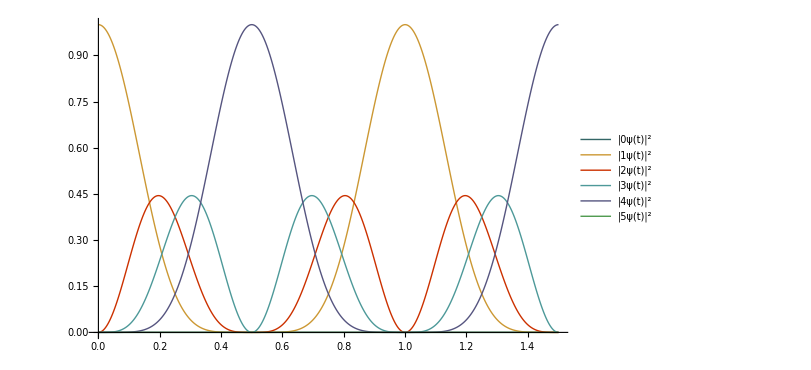

```mathematica
ListLinePlot[{gs,ones,twos,threes,fours,fives},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->600,LabelStyle->Directive[Medium],PlotLegends->ll,PlotStyle->Transpose@{ConstantArray["Thick",Length@ColorData[64,"ColorList"]],ColorData[64,"ColorList"]}]
```

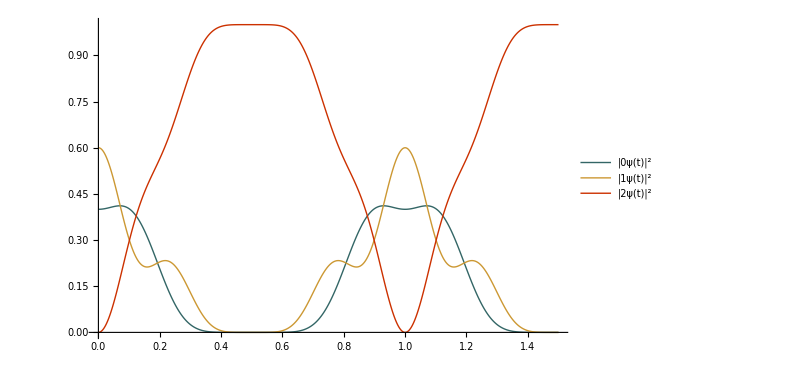

```mathematica
p0s={0.1,0.4,0.5};
ListLinePlot[{
Table[{ts[[i]],p0s.{gsnonW[[i,2]],gsg[[i,2]],gsW[[i,2]]}},{i,Length@ts}],
Table[{ts[[i]],p0s.{onesnonW[[i,2]],onesg[[i,2]],onesW[[i,2]]}},{i,Length@ts}],
Table[{ts[[i]],p0s.{gte2nonW[[i,2]],gte2g[[i,2]],gte2W[[i,2]]}},{i,Length@ts}]
},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->600,LabelStyle->Directive[Medium],PlotLegends->ll,PlotStyle->Transpose@{ConstantArray["Thick",Length@ColorData[64,"ColorList"]],ColorData[64,"ColorList"]},PlotRange->{0,1}]
```

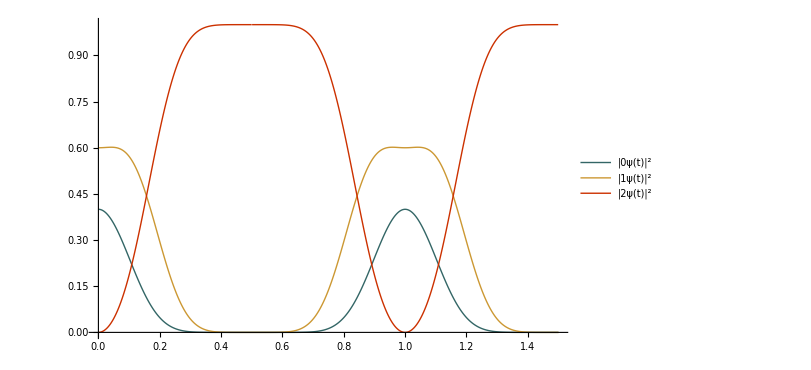

```mathematica
p0s={0.6,0.4,0.};
ListLinePlot[{
Table[{ts[[i]],p0s.{gsnonW[[i,2]],gsg[[i,2]],gsW[[i,2]]}},{i,Length@ts}],
Table[{ts[[i]],p0s.{onesnonW[[i,2]],onesg[[i,2]],onesW[[i,2]]}},{i,Length@ts}],
Table[{ts[[i]],p0s.{gte2nonW[[i,2]],gte2g[[i,2]],gte2W[[i,2]]}},{i,Length@ts}]
},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->600,LabelStyle->Directive[Medium],PlotLegends->ll,PlotStyle->Transpose@{ConstantArray["Thick",Length@ColorData[64,"ColorList"]],ColorData[64,"ColorList"]},PlotRange->{0,1}]
```

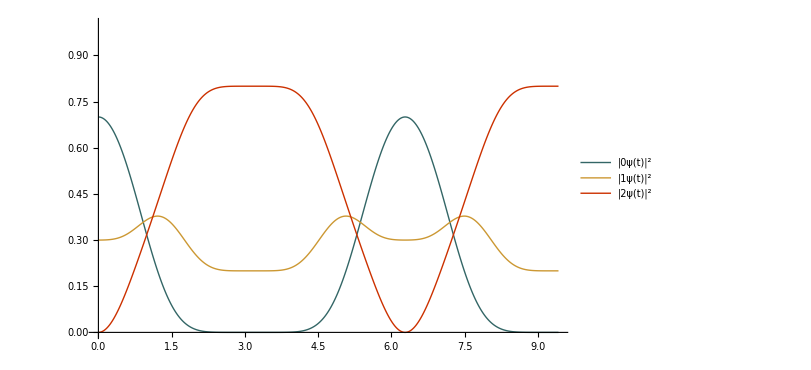

```mathematica
p0s={0.0,0.7,0.3};
ListLinePlot[{
Table[{2π ts[[i]],p0s.{gsnonW[[i,2]],gsg[[i,2]],gsW[[i,2]]}},{i,Length@ts}],
Table[{2π ts[[i]],p0s.{onesnonW[[i,2]],onesg[[i,2]],onesW[[i,2]]}+0.2*p0s.{gte2nonW[[i,2]],gte2g[[i,2]],gte2W[[i,2]]}},{i,Length@ts}],
Table[{2π ts[[i]],0.8*p0s.{gte2nonW[[i,2]],gte2g[[i,2]],gte2W[[i,2]]}},{i,Length@ts}]
},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->600,LabelStyle->Directive[Medium],PlotLegends->ll,PlotStyle->Transpose@{ConstantArray["Thick",Length@ColorData[64,"ColorList"]],ColorData[64,"ColorList"]},PlotRange->{0,1}]
```

```mathematica
gsnonW
```

{{0.,1.},{0.001,0.999951},{0.002,0.999803},{0.003,0.999556},{0.004,0.999211},{0.005,0.998767},{0.006,0.998225},{0.007,0.997585},{0.008,0.996846},{0.009,0.99601},{0.01,0.995077},{0.011,0.994045},{0.012,0.992917},{0.013,0.991693},{0.014,0.990371},{0.015,0.988954},{0.016,0.987441},{0.017,0.985833},{0.018,0.98413},{0.019,0.982333},{0.02,0.980442},{0.021,0.978457},{0.022,0.97638},{0.023,0.974211},{0.024,0.971949},{0.025,0.969597},{0.026,0.967155},{0.027,0.964623},{0.028,0.962002},{0.029,0.959293},{0.03,0.956496},{0.031,0.953612},{0.032,0.950642},{0.033,0.947587},{0.034,0.944448},{0.035,0.941225},{0.036,0.937919},{0.037,0.934531},{0.038,0.931063},{0.039,0.927514},{0.04,0.923887},{0.041,0.920181},{0.042,0.916399},{0.043,0.91254},{0.044,0.908606},{0.045,0.904598},{0.046,0.900517},{0.047,0.896364},{0.048,0.892141},{0.049,0.887847},{0.05,0.883485},{0.051,0.879056},{0.052,0.87456},{0.053,0.869998},{0.054,0.865373},{0.055,0.860685},{0.056,0.855935},{0.057,0.851125},{0.058,0.846256},{0.059,0.841328},{0.06,0.836344},{0.061,0.831305},{0.062,0.826211},{0.063,0.821064},{0.064,0.815865},{0.065,0.810616},{0.066,0.805318},{0.067,0.799972},{0.068,0.794579},{0.069,0.789142},{0.07,0.78366},{0.071,0.778136},{0.072,0.772571},{0.073,0.766965},{0.074,0.761321},{0.075,0.75564},{0.076,0.749923},{0.077,0.744172},{0.078,0.738387},{0.079,0.732571},{0.08,0.726723},{0.081,0.720847},{0.082,0.714943},{0.083,0.709012},{0.084,0.703057},{0.085,0.697077},{0.086,0.691075},{0.087,0.685052},{0.088,0.679009},{0.089,0.672948},{0.09,0.666869},{0.091,0.660775},{0.092,0.654666},{0.093,0.648544},{0.094,0.64241},{0.095,0.636266},{0.096,0.630112},{0.097,0.62395},{0.098,0.617781},{0.099,0.611607},{0.1,0.605429},{0.101,0.599248},{0.102,0.593065},{0.103,0.586881},{0.104,0.580698},{0.105,0.574517},{0.106,0.56834},{0.107,0.562166},{0.108,0.555998},{0.109,0.549837},{0.11,0.543683},{0.111,0.537539},{0.112,0.531404},{0.113,0.525281},{0.114,0.519169},{0.115,0.513072},{0.116,0.506988},{0.117,0.500921},{0.118,0.494869},{0.119,0.488836},{0.12,0.48282},{0.121,0.476825},{0.122,0.47085},{0.123,0.464896},{0.124,0.458965},{0.125,0.453058},{0.126,0.447174},{0.127,0.441316},{0.128,0.435484},{0.129,0.429679},{0.13,0.423902},{0.131,0.418154},{0.132,0.412435},{0.133,0.406746},{0.134,0.401089},{0.135,0.395463},{0.136,0.38987},{0.137,0.38431},{0.138,0.378784},{0.139,0.373293},{0.14,0.367837},{0.141,0.362418},{0.142,0.357035},{0.143,0.351689},{0.144,0.346381},{0.145,0.341112},{0.146,0.335882},{0.147,0.330691},{0.148,0.32554},{0.149,0.32043},{0.15,0.315362},{0.151,0.310334},{0.152,0.305349},{0.153,0.300407},{0.154,0.295507},{0.155,0.290651},{0.156,0.285838},{0.157,0.281069},{0.158,0.276345},{0.159,0.271665},{0.16,0.267031},{0.161,0.262442},{0.162,0.257898},{0.163,0.2534},{0.164,0.248949},{0.165,0.244543},{0.166,0.240185},{0.167,0.235873},{0.168,0.231607},{0.169,0.227389},{0.17,0.223218},{0.171,0.219095},{0.172,0.215019},{0.173,0.21099},{0.174,0.207009},{0.175,0.203076},{0.176,0.19919},{0.177,0.195352},{0.178,0.191562},{0.179,0.187819},{0.18,0.184124},{0.181,0.180477},{0.182,0.176878},{0.183,0.173326},{0.184,0.169822},{0.185,0.166365},{0.186,0.162955},{0.187,0.159593},{0.188,0.156278},{0.189,0.15301},{0.19,0.149788},{0.191,0.146614},{0.192,0.143485},{0.193,0.140404},{0.194,0.137368},{0.195,0.134378},{0.196,0.131434},{0.197,0.128535},{0.198,0.125682},{0.199,0.122873},{0.2,0.120109},{0.201,0.11739},{0.202,0.114715},{0.203,0.112084},{0.204,0.109496},{0.205,0.106952},{0.206,0.10445},{0.207,0.101992},{0.208,0.0995755},{0.209,0.0972013},{0.21,0.0948687},{0.211,0.0925775},{0.212,0.0903273},{0.213,0.0881177},{0.214,0.0859483},{0.215,0.0838189},{0.216,0.0817289},{0.217,0.0796781},{0.218,0.0776661},{0.219,0.0756924},{0.22,0.0737566},{0.221,0.0718584},{0.222,0.0699974},{0.223,0.0681731},{0.224,0.0663852},{0.225,0.0646331},{0.226,0.0629166},{0.227,0.0612351},{0.228,0.0595883},{0.229,0.0579757},{0.23,0.056397},{0.231,0.0548516},{0.232,0.0533391},{0.233,0.0518591},{0.234,0.0504112},{0.235,0.048995},{0.236,0.0476099},{0.237,0.0462556},{0.238,0.0449317},{0.239,0.0436376},{0.24,0.0423729},{0.241,0.0411373},{0.242,0.0399302},{0.243,0.0387513},{0.244,0.0376001},{0.245,0.0364761},{0.246,0.035379},{0.247,0.0343082},{0.248,0.0332634},{0.249,0.0322442},{0.25,0.03125},{0.251,0.0302805},{0.252,0.0293353},{0.253,0.0284139},{0.254,0.0275159},{0.255,0.0266409},{0.256,0.0257884},{0.257,0.0249581},{0.258,0.0241496},{0.259,0.0233624},{0.26,0.0225961},{0.261,0.0218504},{0.262,0.0211247},{0.263,0.0204189},{0.264,0.0197323},{0.265,0.0190648},{0.266,0.0184158},{0.267,0.017785},{0.268,0.017172},{0.269,0.0165764},{0.27,0.0159979},{0.271,0.0154361},{0.272,0.0148907},{0.273,0.0143612},{0.274,0.0138474},{0.275,0.0133489},{0.276,0.0128653},{0.277,0.0123962},{0.278,0.0119415},{0.279,0.0115007},{0.28,0.0110735},{0.281,0.0106595},{0.282,0.0102586},{0.283,0.00987025},{0.284,0.00949427},{0.285,0.00913032},{0.286,0.00877811},{0.287,0.00843733},{0.288,0.00810771},{0.289,0.00778895},{0.29,0.00748077},{0.291,0.0071829},{0.292,0.00689506},{0.293,0.00661699},{0.294,0.00634842},{0.295,0.0060891},{0.296,0.00583877},{0.297,0.00559719},{0.298,0.00536412},{0.299,0.0051393},{0.3,0.00492251},{0.301,0.00471352},{0.302,0.00451211},{0.303,0.00431804},{0.304,0.00413111},{0.305,0.0039511},{0.306,0.00377781},{0.307,0.00361103},{0.308,0.00345056},{0.309,0.00329622},{0.31,0.0031478},{0.311,0.00300513},{0.312,0.00286802},{0.313,0.00273629},{0.314,0.00260978},{0.315,0.00248831},{0.316,0.00237171},{0.317,0.00225983},{0.318,0.00215251},{0.319,0.0020496},{0.32,0.00195094},{0.321,0.00185639},{0.322,0.00176582},{0.323,0.00167907},{0.324,0.00159602},{0.325,0.00151653},{0.326,0.00144048},{0.327,0.00136775},{0.328,0.00129821},{0.329,0.00123174},{0.33,0.00116824},{0.331,0.00110759},{0.332,0.00104968},{0.333,0.000994415},{0.334,0.000941689},{0.335,0.000891403},{0.336,0.000843464},{0.337,0.000797779},{0.338,0.000754257},{0.339,0.000712814},{0.34,0.000673365},{0.341,0.000635828},{0.342,0.000600126},{0.343,0.000566182},{0.344,0.000533923},{0.345,0.000503277},{0.346,0.000474177},{0.347,0.000446555},{0.348,0.000420349},{0.349,0.000395495},{0.35,0.000371936},{0.351,0.000349612},{0.352,0.000328468},{0.353,0.000308452},{0.354,0.000289512},{0.355,0.000271598},{0.356,0.000254662},{0.357,0.00023866},{0.358,0.000223545},{0.359,0.000209277},{0.36,0.000195815},{0.361,0.000183118},{0.362,0.000171151},{0.363,0.000159876},{0.364,0.000149259},{0.365,0.000139268},{0.366,0.000129869},{0.367,0.000121033},{0.368,0.000112731},{0.369,0.000104934},{0.37,0.0000976164},{0.371,0.0000907522},{0.372,0.0000843172},{0.373,0.000078288},{0.374,0.0000726424},{0.375,0.0000673592},{0.376,0.0000624181},{0.377,0.0000577999},{0.378,0.0000534863},{0.379,0.0000494596},{0.38,0.0000457033},{0.381,0.0000422016},{0.382,0.0000389393},{0.383,0.0000359022},{0.384,0.0000330767},{0.385,0.0000304498},{0.386,0.0000280095},{0.387,0.0000257441},{0.388,0.0000236425},{0.389,0.0000216945},{0.39,0.0000198902},{0.391,0.0000182202},{0.392,0.0000166759},{0.393,0.0000152488},{0.394,0.0000139313},{0.395,0.0000127158},{0.396,0.0000115954},{0.397,0.0000105637},{0.398,9.61434×10^-6},{0.399,8.74162×10^-6},{0.4,7.94006×10^-6},{0.401,7.20455×10^-6},{0.402,6.53028×10^-6},{0.403,5.91276×10^-6},{0.404,5.34777×10^-6},{0.405,4.83135×10^-6},{0.406,4.35983×10^-6},{0.407,3.92974×10^-6},{0.408,3.53787×10^-6},{0.409,3.18121×10^-6},{0.41,2.85696×10^-6},{0.411,2.5625×10^-6},{0.412,2.29542×10^-6},{0.413,2.05345×10^-6},{0.414,1.8345×10^-6},{0.415,1.63663×10^-6},{0.416,1.45803×10^-6},{0.417,1.29704×10^-6},{0.418,1.15211×10^-6},{0.419,1.02182×10^-6},{0.42,9.0486×10^-7},{0.421,8.00005×10^-7},{0.422,7.06145×10^-7},{0.423,6.22253×10^-7},{0.424,5.47385×10^-7},{0.425,4.80676×10^-7},{0.426,4.21333×10^-7},{0.427,3.6863×10^-7},{0.428,3.21904×10^-7},{0.429,2.8055×10^-7},{0.43,2.44016×10^-7},{0.431,2.11799×10^-7},{0.432,1.83444×10^-7},{0.433,1.58537×10^-7},{0.434,1.36702×10^-7},{0.435,1.176×10^-7},{0.436,1.00925×10^-7},{0.437,8.63999×10^-8},{0.438,7.37768×10^-8},{0.439,6.28322×10^-8},{0.44,5.33658×10^-8},{0.441,4.51983×10^-8},{0.442,3.81698×10^-8},{0.443,3.21375×10^-8},{0.444,2.69745×10^-8},{0.445,2.2568×10^-8},{0.446,1.88185×10^-8},{0.447,1.56377×10^-8},{0.448,1.29479×10^-8},{0.449,1.06808×10^-8},{0.45,8.77656×10^-9},{0.451,7.1828×10^-9},{0.452,5.85382×10^-9},{0.453,4.74991×10^-9},{0.454,3.83663×10^-9},{0.455,3.08424×10^-9},{0.456,2.4671×10^-9},{0.457,1.96321×10^-9},{0.458,1.55376×10^-9},{0.459,1.22271×10^-9},{0.46,9.5645×10^-10},{0.461,7.43487×10^-10},{0.462,5.74135×10^-10},{0.463,4.40283×10^-10},{0.464,3.35167×10^-10},{0.465,2.53177×10^-10},{0.466,1.89682×10^-10},{0.467,1.40882×10^-10},{0.468,1.03677×10^-10},{0.469,7.55524×10^-11},{0.47,5.44854×10^-11},{0.471,3.8857×10^-11},{0.472,2.73827×10^-11},{0.473,1.90514×10^-11},{0.474,1.30738×10^-11},{0.475,8.83961×10^-12},{0.476,5.8816×10^-12},{0.477,3.84589×10^-12},{0.478,2.46756×10^-12},{0.479,1.55075×10^-12},{0.48,9.52666×10^-13},{0.481,5.70763×10^-13},{0.482,3.3259×10^-13},{0.483,1.87898×10^-13},{0.484,1.02534×10^-13},{0.485,5.38027×10^-14},{0.486,2.70009×10^-14},{0.487,1.28743×10^-14},{0.488,5.78472×10^-15},{0.489,2.42416×10^-15},{0.49,9.34941×10^-16},{0.491,3.26096×10^-16},{0.492,1.00448×10^-16},{0.493,2.64319×10^-17},{0.494,5.65919×10^-18},{0.495,9.14156×10^-19},{0.496,9.81714×10^-20},{0.497,5.52899×10^-21},{0.498,9.5889×10^-23},{0.499,9.37008×10^-26},{0.5,4.81482×10^-35},{0.501,9.37114×10^-26},{0.502,9.58913×10^-23},{0.503,5.529×10^-21},{0.504,9.81713×10^-20},{0.505,9.14155×10^-19},{0.506,5.65919×10^-18},{0.507,2.64319×10^-17},{0.508,1.00448×10^-16},{0.509,3.26096×10^-16},{0.51,9.34941×10^-16},{0.511,2.42416×10^-15},{0.512,5.78472×10^-15},{0.513,1.28743×10^-14},{0.514,2.70009×10^-14},{0.515,5.38027×10^-14},{0.516,1.02534×10^-13},{0.517,1.87898×10^-13},{0.518,3.3259×10^-13},{0.519,5.70763×10^-13},{0.52,9.52666×10^-13},{0.521,1.55075×10^-12},{0.522,2.46756×10^-12},{0.523,3.84589×10^-12},{0.524,5.8816×10^-12},{0.525,8.83961×10^-12},{0.526,1.30738×10^-11},{0.527,1.90514×10^-11},{0.528,2.73827×10^-11},{0.529,3.8857×10^-11},{0.53,5.44854×10^-11},{0.531,7.55524×10^-11},{0.532,1.03677×10^-10},{0.533,1.40882×10^-10},{0.534,1.89682×10^-10},{0.535,2.53177×10^-10},{0.536,3.35167×10^-10},{0.537,4.40283×10^-10},{0.538,5.74135×10^-10},{0.539,7.43487×10^-10},{0.54,9.5645×10^-10},{0.541,1.22271×10^-9},{0.542,1.55376×10^-9},{0.543,1.96321×10^-9},{0.544,2.4671×10^-9},{0.545,3.08424×10^-9},{0.546,3.83663×10^-9},{0.547,4.74991×10^-9},{0.548,5.85382×10^-9},{0.549,7.1828×10^-9},{0.55,8.77656×10^-9},{0.551,1.06808×10^-8},{0.552,1.29479×10^-8},{0.553,1.56377×10^-8},{0.554,1.88185×10^-8},{0.555,2.2568×10^-8},{0.556,2.69745×10^-8},{0.557,3.21375×10^-8},{0.558,3.81698×10^-8},{0.559,4.51983×10^-8},{0.56,5.33658×10^-8},{0.561,6.28322×10^-8},{0.562,7.37768×10^-8},{0.563,8.63999×10^-8},{0.564,1.00925×10^-7},{0.565,1.176×10^-7},{0.566,1.36702×10^-7},{0.567,1.58537×10^-7},{0.568,1.83444×10^-7},{0.569,2.11799×10^-7},{0.57,2.44016×10^-7},{0.571,2.8055×10^-7},{0.572,3.21904×10^-7},{0.573,3.6863×10^-7},{0.574,4.21333×10^-7},{0.575,4.80676×10^-7},{0.576,5.47385×10^-7},{0.577,6.22253×10^-7},{0.578,7.06145×10^-7},{0.579,8.00005×10^-7},{0.58,9.0486×10^-7},{0.581,1.02182×10^-6},{0.582,1.15211×10^-6},{0.583,1.29704×10^-6},{0.584,1.45803×10^-6},{0.585,1.63663×10^-6},{0.586,1.8345×10^-6},{0.587,2.05345×10^-6},{0.588,2.29542×10^-6},{0.589,2.5625×10^-6},{0.59,2.85696×10^-6},{0.591,3.18121×10^-6},{0.592,3.53787×10^-6},{0.593,3.92974×10^-6},{0.594,4.35983×10^-6},{0.595,4.83135×10^-6},{0.596,5.34777×10^-6},{0.597,5.91276×10^-6},{0.598,6.53028×10^-6},{0.599,7.20455×10^-6},{0.6,7.94006×10^-6},{0.601,8.74162×10^-6},{0.602,9.61434×10^-6},{0.603,0.0000105637},{0.604,0.0000115954},{0.605,0.0000127158},{0.606,0.0000139313},{0.607,0.0000152488},{0.608,0.0000166759},{0.609,0.0000182202},{0.61,0.0000198902},{0.611,0.0000216945},{0.612,0.0000236425},{0.613,0.0000257441},{0.614,0.0000280095},{0.615,0.0000304498},{0.616,0.0000330767},{0.617,0.0000359022},{0.618,0.0000389393},{0.619,0.0000422016},{0.62,0.0000457033},{0.621,0.0000494596},{0.622,0.0000534863},{0.623,0.0000577999},{0.624,0.0000624181},{0.625,0.0000673592},{0.626,0.0000726424},{0.627,0.000078288},{0.628,0.0000843172},{0.629,0.0000907522},{0.63,0.0000976164},{0.631,0.000104934},{0.632,0.000112731},{0.633,0.000121033},{0.634,0.000129869},{0.635,0.000139268},{0.636,0.000149259},{0.637,0.000159876},{0.638,0.000171151},{0.639,0.000183118},{0.64,0.000195815},{0.641,0.000209277},{0.642,0.000223545},{0.643,0.00023866},{0.644,0.000254662},{0.645,0.000271598},{0.646,0.000289512},{0.647,0.000308452},{0.648,0.000328468},{0.649,0.000349612},{0.65,0.000371936},{0.651,0.000395495},{0.652,0.000420349},{0.653,0.000446555},{0.654,0.000474177},{0.655,0.000503277},{0.656,0.000533923},{0.657,0.000566182},{0.658,0.000600126},{0.659,0.000635828},{0.66,0.000673365},{0.661,0.000712814},{0.662,0.000754257},{0.663,0.000797779},{0.664,0.000843464},{0.665,0.000891403},{0.666,0.000941689},{0.667,0.000994415},{0.668,0.00104968},{0.669,0.00110759},{0.67,0.00116824},{0.671,0.00123174},{0.672,0.00129821},{0.673,0.00136775},{0.674,0.00144048},{0.675,0.00151653},{0.676,0.00159602},{0.677,0.00167907},{0.678,0.00176582},{0.679,0.00185639},{0.68,0.00195094},{0.681,0.0020496},{0.682,0.00215251},{0.683,0.00225983},{0.684,0.00237171},{0.685,0.00248831},{0.686,0.00260978},{0.687,0.00273629},{0.688,0.00286802},{0.689,0.00300513},{0.69,0.0031478},{0.691,0.00329622},{0.692,0.00345056},{0.693,0.00361103},{0.694,0.00377781},{0.695,0.0039511},{0.696,0.00413111},{0.697,0.00431804},{0.698,0.00451211},{0.699,0.00471352},{0.7,0.00492251},{0.701,0.0051393},{0.702,0.00536412},{0.703,0.00559719},{0.704,0.00583877},{0.705,0.0060891},{0.706,0.00634842},{0.707,0.00661699},{0.708,0.00689506},{0.709,0.0071829},{0.71,0.00748077},{0.711,0.00778895},{0.712,0.00810771},{0.713,0.00843733},{0.714,0.00877811},{0.715,0.00913032},{0.716,0.00949427},{0.717,0.00987025},{0.718,0.0102586},{0.719,0.0106595},{0.72,0.0110735},{0.721,0.0115007},{0.722,0.0119415},{0.723,0.0123962},{0.724,0.0128653},{0.725,0.0133489},{0.726,0.0138474},{0.727,0.0143612},{0.728,0.0148907},{0.729,0.0154361},{0.73,0.0159979},{0.731,0.0165764},{0.732,0.017172},{0.733,0.017785},{0.734,0.0184158},{0.735,0.0190648},{0.736,0.0197323},{0.737,0.0204189},{0.738,0.0211247},{0.739,0.0218504},{0.74,0.0225961},{0.741,0.0233624},{0.742,0.0241496},{0.743,0.0249581},{0.744,0.0257884},{0.745,0.0266409},{0.746,0.0275159},{0.747,0.0284139},{0.748,0.0293353},{0.749,0.0302805},{0.75,0.03125},{0.751,0.0322442},{0.752,0.0332634},{0.753,0.0343082},{0.754,0.035379},{0.755,0.0364761},{0.756,0.0376001},{0.757,0.0387513},{0.758,0.0399302},{0.759,0.0411373},{0.76,0.0423729},{0.761,0.0436376},{0.762,0.0449317},{0.763,0.0462556},{0.764,0.0476099},{0.765,0.048995},{0.766,0.0504112},{0.767,0.0518591},{0.768,0.0533391},{0.769,0.0548516},{0.77,0.056397},{0.771,0.0579757},{0.772,0.0595883},{0.773,0.0612351},{0.774,0.0629166},{0.775,0.0646331},{0.776,0.0663852},{0.777,0.0681731},{0.778,0.0699974},{0.779,0.0718584},{0.78,0.0737566},{0.781,0.0756924},{0.782,0.0776661},{0.783,0.0796781},{0.784,0.0817289},{0.785,0.0838189},{0.786,0.0859483},{0.787,0.0881177},{0.788,0.0903273},{0.789,0.0925775},{0.79,0.0948687},{0.791,0.0972013},{0.792,0.0995755},{0.793,0.101992},{0.794,0.10445},{0.795,0.106952},{0.796,0.109496},{0.797,0.112084},{0.798,0.114715},{0.799,0.11739},{0.8,0.120109},{0.801,0.122873},{0.802,0.125682},{0.803,0.128535},{0.804,0.131434},{0.805,0.134378},{0.806,0.137368},{0.807,0.140404},{0.808,0.143485},{0.809,0.146614},{0.81,0.149788},{0.811,0.15301},{0.812,0.156278},{0.813,0.159593},{0.814,0.162955},{0.815,0.166365},{0.816,0.169822},{0.817,0.173326},{0.818,0.176878},{0.819,0.180477},{0.82,0.184124},{0.821,0.187819},{0.822,0.191562},{0.823,0.195352},{0.824,0.19919},{0.825,0.203076},{0.826,0.207009},{0.827,0.21099},{0.828,0.215019},{0.829,0.219095},{0.83,0.223218},{0.831,0.227389},{0.832,0.231607},{0.833,0.235873},{0.834,0.240185},{0.835,0.244543},{0.836,0.248949},{0.837,0.2534},{0.838,0.257898},{0.839,0.262442},{0.84,0.267031},{0.841,0.271665},{0.842,0.276345},{0.843,0.281069},{0.844,0.285838},{0.845,0.290651},{0.846,0.295507},{0.847,0.300407},{0.848,0.305349},{0.849,0.310334},{0.85,0.315362},{0.851,0.32043},{0.852,0.32554},{0.853,0.330691},{0.854,0.335882},{0.855,0.341112},{0.856,0.346381},{0.857,0.351689},{0.858,0.357035},{0.859,0.362418},{0.86,0.367837},{0.861,0.373293},{0.862,0.378784},{0.863,0.38431},{0.864,0.38987},{0.865,0.395463},{0.866,0.401089},{0.867,0.406746},{0.868,0.412435},{0.869,0.418154},{0.87,0.423902},{0.871,0.429679},{0.872,0.435484},{0.873,0.441316},{0.874,0.447174},{0.875,0.453058},{0.876,0.458965},{0.877,0.464896},{0.878,0.47085},{0.879,0.476825},{0.88,0.48282},{0.881,0.488836},{0.882,0.494869},{0.883,0.500921},{0.884,0.506988},{0.885,0.513072},{0.886,0.519169},{0.887,0.525281},{0.888,0.531404},{0.889,0.537539},{0.89,0.543683},{0.891,0.549837},{0.892,0.555998},{0.893,0.562166},{0.894,0.56834},{0.895,0.574517},{0.896,0.580698},{0.897,0.586881},{0.898,0.593065},{0.899,0.599248},{0.9,0.605429},{0.901,0.611607},{0.902,0.617781},{0.903,0.62395},{0.904,0.630112},{0.905,0.636266},{0.906,0.64241},{0.907,0.648544},{0.908,0.654666},{0.909,0.660775},{0.91,0.666869},{0.911,0.672948},{0.912,0.679009},{0.913,0.685052},{0.914,0.691075},{0.915,0.697077},{0.916,0.703057},{0.917,0.709012},{0.918,0.714943},{0.919,0.720847},{0.92,0.726723},{0.921,0.732571},{0.922,0.738387},{0.923,0.744172},{0.924,0.749923},{0.925,0.75564},{0.926,0.761321},{0.927,0.766965},{0.928,0.772571},{0.929,0.778136},{0.93,0.78366},{0.931,0.789142},{0.932,0.794579},{0.933,0.799972},{0.934,0.805318},{0.935,0.810616},{0.936,0.815865},{0.937,0.821064},{0.938,0.826211},{0.939,0.831305},{0.94,0.836344},{0.941,0.841328},{0.942,0.846256},{0.943,0.851125},{0.944,0.855935},{0.945,0.860685},{0.946,0.865373},{0.947,0.869998},{0.948,0.87456},{0.949,0.879056},{0.95,0.883485},{0.951,0.887847},{0.952,0.892141},{0.953,0.896364},{0.954,0.900517},{0.955,0.904598},{0.956,0.908606},{0.957,0.91254},{0.958,0.916399},{0.959,0.920181},{0.96,0.923887},{0.961,0.927514},{0.962,0.931063},{0.963,0.934531},{0.964,0.937919},{0.965,0.941225},{0.966,0.944448},{0.967,0.947587},{0.968,0.950642},{0.969,0.953612},{0.97,0.956496},{0.971,0.959293},{0.972,0.962002},{0.973,0.964623},{0.974,0.967155},{0.975,0.969597},{0.976,0.971949},{0.977,0.974211},{0.978,0.97638},{0.979,0.978457},{0.98,0.980442},{0.981,0.982333},{0.982,0.98413},{0.983,0.985833},{0.984,0.987441},{0.985,0.988954},{0.986,0.990371},{0.987,0.991693},{0.988,0.992917},{0.989,0.994045},{0.99,0.995077},{0.991,0.99601},{0.992,0.996846},{0.993,0.997585},{0.994,0.998225},{0.995,0.998767},{0.996,0.999211},{0.997,0.999556},{0.998,0.999803},{0.999,0.999951},{1.,1.},{1.001,0.999951},{1.002,0.999803},{1.003,0.999556},{1.004,0.999211},{1.005,0.998767},{1.006,0.998225},{1.007,0.997585},{1.008,0.996846},{1.009,0.99601},{1.01,0.995077},{1.011,0.994045},{1.012,0.992917},{1.013,0.991693},{1.014,0.990371},{1.015,0.988954},{1.016,0.987441},{1.017,0.985833},{1.018,0.98413},{1.019,0.982333},{1.02,0.980442},{1.021,0.978457},{1.022,0.97638},{1.023,0.974211},{1.024,0.971949},{1.025,0.969597},{1.026,0.967155},{1.027,0.964623},{1.028,0.962002},{1.029,0.959293},{1.03,0.956496},{1.031,0.953612},{1.032,0.950642},{1.033,0.947587},{1.034,0.944448},{1.035,0.941225},{1.036,0.937919},{1.037,0.934531},{1.038,0.931063},{1.039,0.927514},{1.04,0.923887},{1.041,0.920181},{1.042,0.916399},{1.043,0.91254},{1.044,0.908606},{1.045,0.904598},{1.046,0.900517},{1.047,0.896364},{1.048,0.892141},{1.049,0.887847},{1.05,0.883485},{1.051,0.879056},{1.052,0.87456},{1.053,0.869998},{1.054,0.865373},{1.055,0.860685},{1.056,0.855935},{1.057,0.851125},{1.058,0.846256},{1.059,0.841328},{1.06,0.836344},{1.061,0.831305},{1.062,0.826211},{1.063,0.821064},{1.064,0.815865},{1.065,0.810616},{1.066,0.805318},{1.067,0.799972},{1.068,0.794579},{1.069,0.789142},{1.07,0.78366},{1.071,0.778136},{1.072,0.772571},{1.073,0.766965},{1.074,0.761321},{1.075,0.75564},{1.076,0.749923},{1.077,0.744172},{1.078,0.738387},{1.079,0.732571},{1.08,0.726723},{1.081,0.720847},{1.082,0.714943},{1.083,0.709012},{1.084,0.703057},{1.085,0.697077},{1.086,0.691075},{1.087,0.685052},{1.088,0.679009},{1.089,0.672948},{1.09,0.666869},{1.091,0.660775},{1.092,0.654666},{1.093,0.648544},{1.094,0.64241},{1.095,0.636266},{1.096,0.630112},{1.097,0.62395},{1.098,0.617781},{1.099,0.611607},{1.1,0.605429},{1.101,0.599248},{1.102,0.593065},{1.103,0.586881},{1.104,0.580698},{1.105,0.574517},{1.106,0.56834},{1.107,0.562166},{1.108,0.555998},{1.109,0.549837},{1.11,0.543683},{1.111,0.537539},{1.112,0.531404},{1.113,0.525281},{1.114,0.519169},{1.115,0.513072},{1.116,0.506988},{1.117,0.500921},{1.118,0.494869},{1.119,0.488836},{1.12,0.48282},{1.121,0.476825},{1.122,0.47085},{1.123,0.464896},{1.124,0.458965},{1.125,0.453058},{1.126,0.447174},{1.127,0.441316},{1.128,0.435484},{1.129,0.429679},{1.13,0.423902},{1.131,0.418154},{1.132,0.412435},{1.133,0.406746},{1.134,0.401089},{1.135,0.395463},{1.136,0.38987},{1.137,0.38431},{1.138,0.378784},{1.139,0.373293},{1.14,0.367837},{1.141,0.362418},{1.142,0.357035},{1.143,0.351689},{1.144,0.346381},{1.145,0.341112},{1.146,0.335882},{1.147,0.330691},{1.148,0.32554},{1.149,0.32043},{1.15,0.315362},{1.151,0.310334},{1.152,0.305349},{1.153,0.300407},{1.154,0.295507},{1.155,0.290651},{1.156,0.285838},{1.157,0.281069},{1.158,0.276345},{1.159,0.271665},{1.16,0.267031},{1.161,0.262442},{1.162,0.257898},{1.163,0.2534},{1.164,0.248949},{1.165,0.244543},{1.166,0.240185},{1.167,0.235873},{1.168,0.231607},{1.169,0.227389},{1.17,0.223218},{1.171,0.219095},{1.172,0.215019},{1.173,0.21099},{1.174,0.207009},{1.175,0.203076},{1.176,0.19919},{1.177,0.195352},{1.178,0.191562},{1.179,0.187819},{1.18,0.184124},{1.181,0.180477},{1.182,0.176878},{1.183,0.173326},{1.184,0.169822},{1.185,0.166365},{1.186,0.162955},{1.187,0.159593},{1.188,0.156278},{1.189,0.15301},{1.19,0.149788},{1.191,0.146614},{1.192,0.143485},{1.193,0.140404},{1.194,0.137368},{1.195,0.134378},{1.196,0.131434},{1.197,0.128535},{1.198,0.125682},{1.199,0.122873},{1.2,0.120109},{1.201,0.11739},{1.202,0.114715},{1.203,0.112084},{1.204,0.109496},{1.205,0.106952},{1.206,0.10445},{1.207,0.101992},{1.208,0.0995755},{1.209,0.0972013},{1.21,0.0948687},{1.211,0.0925775},{1.212,0.0903273},{1.213,0.0881177},{1.214,0.0859483},{1.215,0.0838189},{1.216,0.0817289},{1.217,0.0796781},{1.218,0.0776661},{1.219,0.0756924},{1.22,0.0737566},{1.221,0.0718584},{1.222,0.0699974},{1.223,0.0681731},{1.224,0.0663852},{1.225,0.0646331},{1.226,0.0629166},{1.227,0.0612351},{1.228,0.0595883},{1.229,0.0579757},{1.23,0.056397},{1.231,0.0548516},{1.232,0.0533391},{1.233,0.0518591},{1.234,0.0504112},{1.235,0.048995},{1.236,0.0476099},{1.237,0.0462556},{1.238,0.0449317},{1.239,0.0436376},{1.24,0.0423729},{1.241,0.0411373},{1.242,0.0399302},{1.243,0.0387513},{1.244,0.0376001},{1.245,0.0364761},{1.246,0.035379},{1.247,0.0343082},{1.248,0.0332634},{1.249,0.0322442},{1.25,0.03125},{1.251,0.0302805},{1.252,0.0293353},{1.253,0.0284139},{1.254,0.0275159},{1.255,0.0266409},{1.256,0.0257884},{1.257,0.0249581},{1.258,0.0241496},{1.259,0.0233624},{1.26,0.0225961},{1.261,0.0218504},{1.262,0.0211247},{1.263,0.0204189},{1.264,0.0197323},{1.265,0.0190648},{1.266,0.0184158},{1.267,0.017785},{1.268,0.017172},{1.269,0.0165764},{1.27,0.0159979},{1.271,0.0154361},{1.272,0.0148907},{1.273,0.0143612},{1.274,0.0138474},{1.275,0.0133489},{1.276,0.0128653},{1.277,0.0123962},{1.278,0.0119415},{1.279,0.0115007},{1.28,0.0110735},{1.281,0.0106595},{1.282,0.0102586},{1.283,0.00987025},{1.284,0.00949427},{1.285,0.00913032},{1.286,0.00877811},{1.287,0.00843733},{1.288,0.00810771},{1.289,0.00778895},{1.29,0.00748077},{1.291,0.0071829},{1.292,0.00689506},{1.293,0.00661699},{1.294,0.00634842},{1.295,0.0060891},{1.296,0.00583877},{1.297,0.00559719},{1.298,0.00536412},{1.299,0.0051393},{1.3,0.00492251},{1.301,0.00471352},{1.302,0.00451211},{1.303,0.00431804},{1.304,0.00413111},{1.305,0.0039511},{1.306,0.00377781},{1.307,0.00361103},{1.308,0.00345056},{1.309,0.00329622},{1.31,0.0031478},{1.311,0.00300513},{1.312,0.00286802},{1.313,0.00273629},{1.314,0.00260978},{1.315,0.00248831},{1.316,0.00237171},{1.317,0.00225983},{1.318,0.00215251},{1.319,0.0020496},{1.32,0.00195094},{1.321,0.00185639},{1.322,0.00176582},{1.323,0.00167907},{1.324,0.00159602},{1.325,0.00151653},{1.326,0.00144048},{1.327,0.00136775},{1.328,0.00129821},{1.329,0.00123174},{1.33,0.00116824},{1.331,0.00110759},{1.332,0.00104968},{1.333,0.000994415},{1.334,0.000941689},{1.335,0.000891403},{1.336,0.000843464},{1.337,0.000797779},{1.338,0.000754257},{1.339,0.000712814},{1.34,0.000673365},{1.341,0.000635828},{1.342,0.000600126},{1.343,0.000566182},{1.344,0.000533923},{1.345,0.000503277},{1.346,0.000474177},{1.347,0.000446555},{1.348,0.000420349},{1.349,0.000395495},{1.35,0.000371936},{1.351,0.000349612},{1.352,0.000328468},{1.353,0.000308452},{1.354,0.000289512},{1.355,0.000271598},{1.356,0.000254662},{1.357,0.00023866},{1.358,0.000223545},{1.359,0.000209277},{1.36,0.000195815},{1.361,0.000183118},{1.362,0.000171151},{1.363,0.000159876},{1.364,0.000149259},{1.365,0.000139268},{1.366,0.000129869},{1.367,0.000121033},{1.368,0.000112731},{1.369,0.000104934},{1.37,0.0000976164},{1.371,0.0000907522},{1.372,0.0000843172},{1.373,0.000078288},{1.374,0.0000726424},{1.375,0.0000673592},{1.376,0.0000624181},{1.377,0.0000577999},{1.378,0.0000534863},{1.379,0.0000494596},{1.38,0.0000457033},{1.381,0.0000422016},{1.382,0.0000389393},{1.383,0.0000359022},{1.384,0.0000330767},{1.385,0.0000304498},{1.386,0.0000280095},{1.387,0.0000257441},{1.388,0.0000236425},{1.389,0.0000216945},{1.39,0.0000198902},{1.391,0.0000182202},{1.392,0.0000166759},{1.393,0.0000152488},{1.394,0.0000139313},{1.395,0.0000127158},{1.396,0.0000115954},{1.397,0.0000105637},{1.398,9.61434×10^-6},{1.399,8.74162×10^-6},{1.4,7.94006×10^-6},{1.401,7.20455×10^-6},{1.402,6.53028×10^-6},{1.403,5.91276×10^-6},{1.404,5.34777×10^-6},{1.405,4.83135×10^-6},{1.406,4.35983×10^-6},{1.407,3.92974×10^-6},{1.408,3.53787×10^-6},{1.409,3.18121×10^-6},{1.41,2.85696×10^-6},{1.411,2.5625×10^-6},{1.412,2.29542×10^-6},{1.413,2.05345×10^-6},{1.414,1.8345×10^-6},{1.415,1.63663×10^-6},{1.416,1.45803×10^-6},{1.417,1.29704×10^-6},{1.418,1.15211×10^-6},{1.419,1.02182×10^-6},{1.42,9.0486×10^-7},{1.421,8.00005×10^-7},{1.422,7.06145×10^-7},{1.423,6.22253×10^-7},{1.424,5.47385×10^-7},{1.425,4.80676×10^-7},{1.426,4.21333×10^-7},{1.427,3.6863×10^-7},{1.428,3.21904×10^-7},{1.429,2.8055×10^-7},{1.43,2.44016×10^-7},{1.431,2.11799×10^-7},{1.432,1.83444×10^-7},{1.433,1.58537×10^-7},{1.434,1.36702×10^-7},{1.435,1.176×10^-7},{1.436,1.00925×10^-7},{1.437,8.63999×10^-8},{1.438,7.37768×10^-8},{1.439,6.28322×10^-8},{1.44,5.33658×10^-8},{1.441,4.51983×10^-8},{1.442,3.81698×10^-8},{1.443,3.21375×10^-8},{1.444,2.69745×10^-8},{1.445,2.2568×10^-8},{1.446,1.88185×10^-8},{1.447,1.56377×10^-8},{1.448,1.29479×10^-8},{1.449,1.06808×10^-8},{1.45,8.77656×10^-9},{1.451,7.1828×10^-9},{1.452,5.85382×10^-9},{1.453,4.74991×10^-9},{1.454,3.83663×10^-9},{1.455,3.08424×10^-9},{1.456,2.4671×10^-9},{1.457,1.96321×10^-9},{1.458,1.55376×10^-9},{1.459,1.22271×10^-9},{1.46,9.5645×10^-10},{1.461,7.43487×10^-10},{1.462,5.74135×10^-10},{1.463,4.40283×10^-10},{1.464,3.35167×10^-10},{1.465,2.53177×10^-10},{1.466,1.89682×10^-10},{1.467,1.40882×10^-10},{1.468,1.03677×10^-10},{1.469,7.55524×10^-11},{1.47,5.44854×10^-11},{1.471,3.8857×10^-11},{1.472,2.73827×10^-11},{1.473,1.90514×10^-11},{1.474,1.30738×10^-11},{1.475,8.83961×10^-12},{1.476,5.8816×10^-12},{1.477,3.84589×10^-12},{1.478,2.46756×10^-12},{1.479,1.55075×10^-12},{1.48,9.52666×10^-13},{1.481,5.70763×10^-13},{1.482,3.3259×10^-13},{1.483,1.87898×10^-13},{1.484,1.02534×10^-13},{1.485,5.38027×10^-14},{1.486,2.70009×10^-14},{1.487,1.28743×10^-14},{1.488,5.78472×10^-15},{1.489,2.42416×10^-15},{1.49,9.34941×10^-16},{1.491,3.26096×10^-16},{1.492,1.00448×10^-16},{1.493,2.64319×10^-17},{1.494,5.65919×10^-18},{1.495,9.14156×10^-19},{1.496,9.81712×10^-20},{1.497,5.52902×10^-21},{1.498,9.5884×10^-23},{1.499,9.34227×10^-26},{1.5,9.43706×10^-33}}

```mathematica
Transpose@{ConstantArray["Thick",Length@ColorData[64,"ColorList"]],ColorData[64,"ColorList"]}
```

{{Thick,Hue[0.5,0.5,0.4]},{Thick,Hue[0.11,0.75,0.8]},{Thick,Hue[0.04,1,0.8]},{Thick,Hue[0.5,0.5,0.6]},{Thick,Hue[0.67,0.33,0.5]},{Thick,Hue[0.33,0.5,0.6]},{Thick,Hue[0,0.67,0.6]},{Thick,Hue[0.17,0.9,0.7]},{Thick,Hue[0,0.5,0.6]},{Thick,Hue[0.17,0.33,0.6]}}

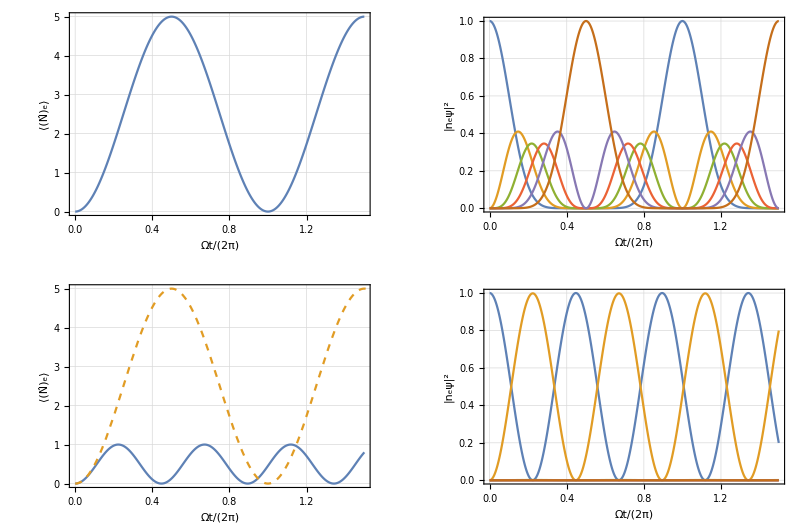

unblockaded_RFE_n=5.pdf

```mathematica
p=GraphicsGrid[{{
Show[
ListLinePlot[
{Transpose@{ts,Total@{ones[[All,2]],2*twos[[All,2]],3*threes[[All,2]],4*fours[[All,2]],5*fives[[All,2]]}}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
]
],
ListLinePlot[{gs,ones,twos,threes,fours,fives},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
ll
},
{
Show[
ListLinePlot[
{Transpose@{tsb,Total@{onesb[[All,2]],2*twosb[[All,2]],3*threesb[[All,2]],4*foursb[[All,2]],5*fivesb[[All,2]]}}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
],
Plot[{,n Sin[π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
ListLinePlot[{gsb,onesb,twosb,threesb,foursb,fivesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
ll
}},ImageSize->800]
SetDirectory[NotebookDirectory[]];
(*Export["unblockaded_RFE_n=5.pdf",p]*)
```

```mathematica
Hbperf=ArrayFlatten@{
{Δb[[1]],a as[[1]]},
{a Transpose[as[[1]]],Δb[[2]]}
}+DiagonalMatrix[{0,1,1,1}]d;
MatrixForm@Hbperf
{e,v}=Eigensystem@Hbperf;
v=v/Norm/@v;
e
v//Chop//MatrixForm
```

(0 | a/2 | a/2 | a/2
a/2 | d | 0 | 0
a/2 | 0 | d | 0
a/2 | 0 | 0 | d)

{d,d,1/2 (d-√(3 a^2+d^2)),1/2 (d+√(3 a^2+d^2))}

(0 | -1/(√2) | 0 | 1/(√2)
0 | -1/(√2) | 1/(√2) | 0
-(d+√(3 a^2+d^2))/(a √(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2))
-(d-√(3 a^2+d^2))/(a √(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)))

```mathematica
n=5;
Hbperf=ArrayFlatten@{
{0,{Table[a[m],{m,n}]}},
{Transpose[{Table[a[m],{m,n}]}],DiagonalMatrix[ConstantArray[0,n]]}
};
MatrixForm@Hbperf
{e,v}=Eigensystem@Hbperf;
v=v/Norm/@v;
e
v//Chop//MatrixForm
```

(0 | a[1] | a[2] | a[3] | a[4] | a[5]
a[1] | 0 | 0 | 0 | 0 | 0
a[2] | 0 | 0 | 0 | 0 | 0
a[3] | 0 | 0 | 0 | 0 | 0
a[4] | 0 | 0 | 0 | 0 | 0
a[5] | 0 | 0 | 0 | 0 | 0)

{0,0,0,0,-√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2),√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2)}

(0 | -a[5]/(a[1] √(1+Abs[a[5]/a[1]]^2)) | 0 | 0 | 0 | 1/(√(1+Abs[a[5]/a[1]]^2))
0 | -a[4]/(a[1] √(1+Abs[a[4]/a[1]]^2)) | 0 | 0 | 1/(√(1+Abs[a[4]/a[1]]^2)) | 0
0 | -a[3]/(a[1] √(1+Abs[a[3]/a[1]]^2)) | 0 | 1/(√(1+Abs[a[3]/a[1]]^2)) | 0 | 0
0 | -a[2]/(a[1] √(1+Abs[a[2]/a[1]]^2)) | 1/(√(1+Abs[a[2]/a[1]]^2)) | 0 | 0 | 0
-(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[1]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[2]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[3]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[4]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | 1/(√(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2))
(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[1]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[2]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[3]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[4]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | 1/(√(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)))

```mathematica
vnew=Orthogonalize[v[[3;;-1]]];
```

```mathematica
Simplify[vnew[[1]],Assumptions->a[1]>0&&a[5]>0]
Simplify[vnew[[2]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
Simplify[vnew[[3]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
Simplify[vnew[[4]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
```

{0,-a[3]/(√(a[1]^2+Abs[a[3]]^2)),0,a[1]/(√(a[1]^2+Abs[a[3]]^2)),0,0}

{0,-(a[1] a[2])/(√((a[1]^2+a[3]^2) (a[1]^2+a[2]^2+a[3]^2))),√((a[1]^2+a[3]^2)/(a[1]^2+a[2]^2+a[3]^2)),-(a[2] a[3])/(√((a[1]^2+a[3]^2) (a[1]^2+a[2]^2+a[3]^2))),0,0}

$Aborted

$Aborted

```mathematica
Hbperf.DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}]-DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}].Hbperf//MatrixForm
```

(0 | a[1] d[1] | a[2] d[2] | a[3] d[3] | a[4] d[4] | a[5] d[5]
-a[1] d[1] | 0 | 0 | 0 | 0 | 0
-a[2] d[2] | 0 | 0 | 0 | 0 | 0
-a[3] d[3] | 0 | 0 | 0 | 0 | 0
-a[4] d[4] | 0 | 0 | 0 | 0 | 0
-a[5] d[5] | 0 | 0 | 0 | 0 | 0)

```mathematica
Hbperf.DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}]//MatrixForm
```

(0 | a[1] d[1] | a[2] d[2] | a[3] d[3] | a[4] d[4] | a[5] d[5]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### What is the correction to the wavefunction for expected numbers

```mathematica
n=5;

beam[p3_,Ω_,w0_,λ_]:=Module[
{w,zR,Rabi},
zR=π w0^2/λ;
w[z_]:=w0 Sqrt[1+(z/zR)^2];
Return[Ω(w0/w[x3[3]-p3[[3]]])Exp[-(((x3[1]-p3[[1]])^2+(x3[2]-p3[[2]])^2)/w[x3[3]-p3[[3]]]^2)]];
];

m=87*1.67*10^-27;
k=1.38*10^-23;

atoms[T_,ω3__]:=Module[{σx3,σv},
σx3=Sqrt[(k T)/(m #^2)]&/@ω3;
σv=Sqrt[(k T)/m];
Return[{σx3,σv}];
];

a=191Sqrt[0.75]; (* 780 Rabi Frequency (both A&B) Scaled with 480 to mimick observed rabi frequency*)
b=19.6Sqrt[0.75]; (* 480 Rabi Frequency Scaled with 480 to mimick observed rabi frequency *)
ΔP=1800; (* Intermediate State Detuning *)
δ=((b^2-a^2)/(4ΔP)); (* Real part of AC Stark Shift that can be accounted for *)
Γ=6; (* Intermediate State Linewidth *)
Ω1=(a b)/(2 ΔP); (* nominal rabi frequency *)
Print["Ω_(2  γ): ",Ω1];
nb=6; (* atom number *)
Δk=(1/.480-1/.780); (* Doppler shift from counter propagating lasers *)

atom=atoms[150*10^-6,{π 0.0829,π 0.0829,2π 0.003185}]; (* atom parameters *)
beam1=beam[{0,0,0},a,8,.780]; (* 780 Beam parameters *)
beam2=beam[{0,0,0},b,4.5,.480]; (* 480 Beam parameters *)

{σx3d,σv}=atom;

trials=10000;
v1fid={};
v2fid={};
v1ortho={};
v2ortho={};
v1v2={};

For[i=1,i≤trials,i+=1,

x3d=RandomVariate[NormalDistribution[0,#],n]&/@σx3d;
vz=RandomVariate[NormalDistribution[0,σv],n]; (* doppler only *)
δdopp=Δk*vz; (* only z contributes to doppler shift *)

(*Print["Doppler: ",δdopp];*)

posSubs=(Table[x3[i]->x3d[[i]],{i,3}]);
α=(beam1/.posSubs);
β=(beam2/.posSubs);

(* calculate the couplings between ground and ryd atoms *)
aas=(α β)/(4(ΔP+I Γ/2));
(*Print["αs: ",aas];*)
GR1={aas};

(* detunings due to inhomogeneous braodening go here *)
Δ1s=(β^2-α^2)/(4(ΔP+I Γ/2))-δdopp-δ;
R1R1=DiagonalMatrix[Δ1s];
(*Print["R1R1: ",MatrixForm[R1R1]];*)

Hbperf=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],R1R1}
};
(*Print["Hb perf: ",MatrixForm[Hbperf]];*)

A=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],DiagonalMatrix[ConstantArray[0,n]]}
};
(*Print["A: ",MatrixForm@A];*)

ΔΔ=ArrayFlatten@{
{0,{ConstantArray[0,n]}},
{Transpose@{ConstantArray[0,n]},R1R1}
};
(*Print["Δ1s: ",MatrixForm@ΔΔ];*)

(*MatrixForm@A*)
{e,v}=Eigensystem@A;
v=Orthogonalize@v;
v=v/Norm/@v;
(*e
v//Chop//MatrixForm*)
{ef,vf}=Eigensystem@Hbperf;
vf=Orthogonalize@vf;
vf=vf/Norm/@vf;
(*ef
vf//Chop//MatrixForm*)

(*Print["v1"];*)
crossovers=Table[Abs[v[[1]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v1fid,Max[crossovers]];
posv1=Ordering[crossovers,-1];

(*Print["v2"];*)
crossovers=Table[Abs[v[[2]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v2fid,Max[crossovers]];
posv2=Ordering[crossovers,-1];

AppendTo[v2ortho,Total[Delete[crossovers,{posv1,posv2}]]];

crossovers=Table[Abs[v[[1]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v1ortho,Total[Delete[crossovers,{posv1,posv2}]]];

AppendTo[v1v2,Abs[v[[posv2[[1]]]].vf[[posv1[[1]]]]]^2];
]
```

Ω_(2  γ): 0.779917

```mathematica
MatrixForm@v//Chop
```

(0.707107 | -0.324438 | -0.312653 | -0.296901 | -0.322754 | -0.323524
0.707107 | 0.324438 | 0.312653 | 0.296901 | 0.322754 | 0.323524
0 | -0.442158-0.000237508 ⅈ | 0.865985 | -0.127263+0.0000770341 ⅈ | -0.138344+0.0000837419 ⅈ | -0.138674+0.0000839417 ⅈ
0 | -0.419881-0.000229347 ⅈ | -0.127263+0.0000758806 ⅈ | 0.879149 | -0.131374+0.000078332 ⅈ | -0.131687+0.0000785189 ⅈ
0 | -0.456443-0.000242344 ⅈ | -0.138344+0.0000846014 ⅈ | -0.131374+0.000080339 ⅈ | 0.857187 | -0.143154+0.000087543 ⅈ
0 | -0.457532-0.0002427 ⅈ | -0.138674+0.0000848709 ⅈ | -0.131687+0.0000805949 ⅈ | -0.143154+0.0000876127 ⅈ | 0.856504)

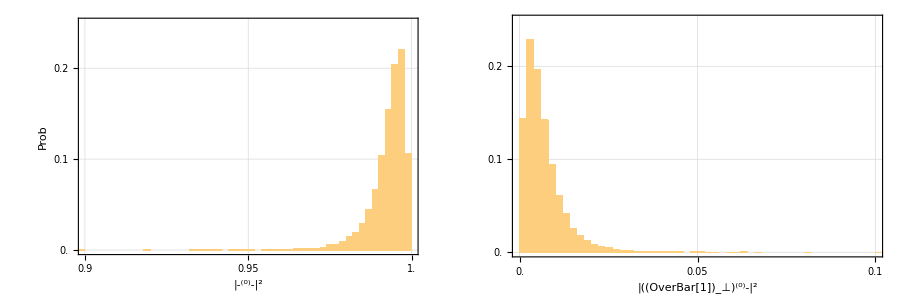

```mathematica
fs=24;
eigenproj=GraphicsRow[{
(Histogram[v2fid,Round@√trials,"Probability",FrameLabel->{"|-^(0)-|^2","Prob"
},ImageSize->Full,PlotRange->{{0.9,1},{0,0.25}},LabelStyle->Directive[Bold, FontSize->fs],FrameTicks->{Range[0.9,1,0.05],Range[0,0.3,0.1],None,None}]),
Histogram[v2ortho,Round@√trials,"Probability",FrameLabel->{"|((OverBar[1])_⊥)^(0)-|^2",""},ImageSize->Full,PlotRange->{{0,0.1},{0,0.25}},LabelStyle->Directive[Bold, FontSize->fs],FrameTicks->{Range[0,.1,0.05],Range[0,0.3,0.1],None,None}]
}
,ImageSize->900]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["eigenstateProj.pdf",eigenproj]
```

eigenstateProj.pdf

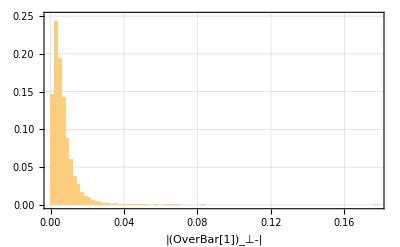

```mathematica
Histogram[v2ortho,Round@√trials,"Probability",FrameLabel->{"|(OverBar[1])_⊥-|",""},ImageSize->400,PlotRange->{0,0.25}]
```

```mathematica
v1v2
```

{0.000634927,0.000107273,0.00168484,0.984839,0.998709,0.995153,0.994303,0.979734,0.99716,0.99442,9980,0.993462,0.0000153194,0.000609609,0.00113965,0.997871,0.000103532,0.0000538167,0.000977754,0.00164463,0.994449}
 |  |  |  |

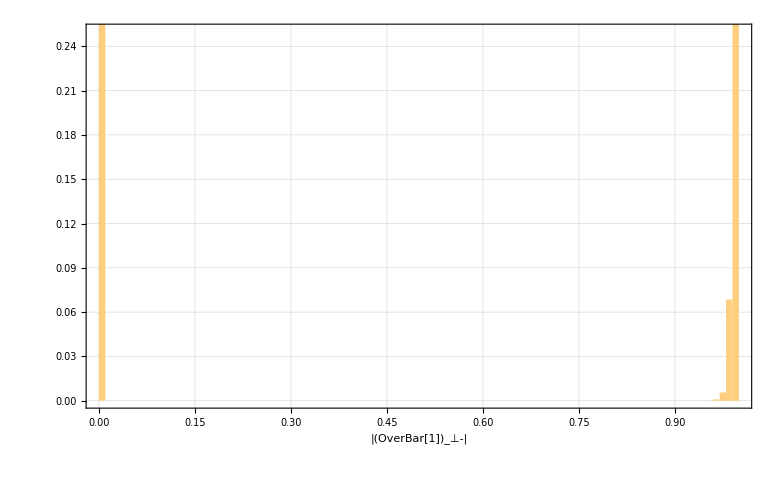

```mathematica
Histogram[v1v2,Round@√trials,"Probability",FrameLabel->{"|(OverBar[1])_⊥-|",""},ImageSize->400,PlotRange->{0,0.25}]
```

```mathematica
(√3)/(√2 √((√3)^2+0.1^2))
```

0.705931

#### expected speed up inhomogeneous broadening correction

```mathematica
n=5;

beam[p3_,Ω_,w0_,λ_]:=Module[
{w,zR,Rabi},
zR=π w0^2/λ;
w[z_]:=w0 Sqrt[1+(z/zR)^2];
Return[Ω(w0/w[x3[3]-p3[[3]]])Exp[-(((x3[1]-p3[[1]])^2+(x3[2]-p3[[2]])^2)/w[x3[3]-p3[[3]]]^2)]];
];

m=87*1.67*10^-27;
k=1.38*10^-23;

atoms[T_,ω3__]:=Module[{σx3,σv},
σx3=Sqrt[(k T)/(m #^2)]&/@ω3;
σv=Sqrt[(k T)/m];
Return[{σx3,σv}];
];

a=191Sqrt[0.75]; (* 780 Rabi Frequency (both A&B) Scaled with 480 to mimick observed rabi frequency*)
b=19.6Sqrt[0.75]; (* 480 Rabi Frequency Scaled with 480 to mimick observed rabi frequency *)
ΔP=1800; (* Intermediate State Detuning *)
δ=((b^2-a^2)/(4ΔP)); (* Real part of AC Stark Shift that can be accounted for *)
Γ=6; (* Intermediate State Linewidth *)
Ω1=(a b)/(2 ΔP); (* nominal rabi frequency *)
Print["Ω_(2  γ): ",Ω1];
nb=6; (* atom number *)
Δk=(1/.480-1/.780); (* Doppler shift from counter propagating lasers *)

atom=atoms[150*10^-6,{π 0.0829,π 0.0829,2π 0.003185}]; (* atom parameters *)
beam1=beam[{0,0,0},a,8,.780]; (* 780 Beam parameters *)
beam2=beam[{0,0,0},b,4.5,.480]; (* 480 Beam parameters *)

{σx3d,σv}=atom;

trials=10000;
es={};
efs={};

For[i=1,i≤trials,i+=1,

x3d=RandomVariate[NormalDistribution[0,#],n]&/@σx3d;
vz=RandomVariate[NormalDistribution[0,σv],n]; (* doppler only *)
δdopp=Δk*vz; (* only z contributes to doppler shift *)

(*Print["Doppler: ",δdopp];*)

posSubs=(Table[x3[i]->x3d[[i]],{i,3}]);
α=(beam1/.posSubs);
β=(beam2/.posSubs);

(* calculate the couplings between ground and ryd atoms *)
aas=(α β)/(4(ΔP+I Γ/2));
(*Print["αs: ",aas];*)
GR1={aas};

(* detunings due to inhomogeneous braodening go here *)
Δ1s=(β^2-α^2)/(4(ΔP+I Γ/2))-δdopp-δ;
R1R1=DiagonalMatrix[Δ1s];
(*Print["R1R1: ",MatrixForm[R1R1]];*)

Hbperf=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],R1R1}
};
(*Print["Hb perf: ",MatrixForm[Hbperf]];*)

A=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],DiagonalMatrix[ConstantArray[0,n]]}
};
(*Print["A: ",MatrixForm@A];*)

ΔΔ=ArrayFlatten@{
{0,{ConstantArray[0,n]}},
{Transpose@{ConstantArray[0,n]},R1R1}
};
(*Print["Δ1s: ",MatrixForm@ΔΔ];*)

(*MatrixForm@A*)
{e,v}=Eigensystem@A;
v=Orthogonalize@v;
v=v/Norm/@v;
(*e
v//Chop//MatrixForm*)
{ef,vf}=Eigensystem@Hbperf;
vf=Orthogonalize@vf;
vf=vf/Norm/@vf;
(*ef
vf//Chop//MatrixForm*)

AppendTo[es,(2{Max[Re@e],Min[Re@e]}/Ω1)^2/n];
AppendTo[efs,(2{Max[Re@ef],Min[Re@ef]}/Ω1)^2/n];
]
```

Ω_(2  γ): 0.779917

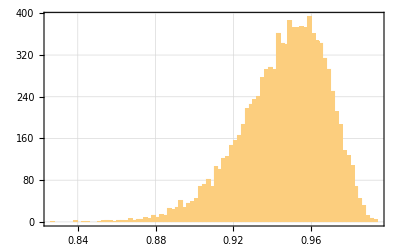

0.945784

0.972514

0.92

0.959166

0.0218473

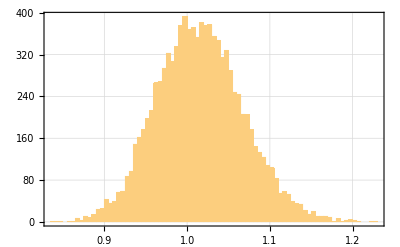

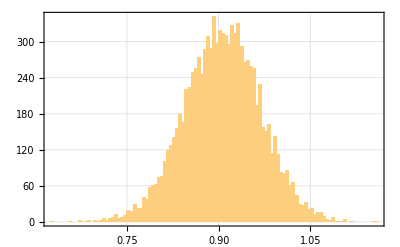

```mathematica
Histogram[es[[All,1]],Round@√trials]
Mean[es[[All,1]]]
Mean[es[[All,1]]]^(1/2)
0.92
0.92^(1/2)
StandardDeviation[es[[All,1]]]
Histogram[efs[[All,1]],Round@√trials]
Histogram[efs[[All,2]],Round@√trials]
```

```mathematica
Eigensystem@ArrayFlatten@{
{0,{ConstantArray[1/2,5]}},
{Transpose[{ConstantArray[1/2,5]}],0}
}
```

{{-(√5)/2,(√5)/2,0,0,0,0},{{-√5,1,1,1,1,1},{√5,1,1,1,1,1},{0,-1,0,0,0,1},{0,-1,0,0,1,0},{0,-1,0,1,0,0},{0,-1,1,0,0,0}}}

#### Time Series for non-symmetric singly excited state

Dot::dotsh: Tensors {0, 1, 1, 1, 0, 0, 0, 0} and {0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ} have incompatible shapes.

Dot::dotsh: Tensors {0, 1, 1, 1, 0, 0, 0, 0} and {4.48957×10^-9 - 0.00544128\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, -0.0000170495 + 7.13767×10^-7\ ⅈ, -0.0000170495 + 7.13767×10^-7\ ⅈ, -0.000453445 - 0.00358944\ ⅈ, « 18 », -5.31566×10^-6 + 1.84992×10^-6\ ⅈ, 3.04899×10^-8 + 4.20602×10^-8\ ⅈ, 3.04899×10^-8 + 4.20602×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 8.47704×10^-11 - 1.32586×10^-10\ ⅈ} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

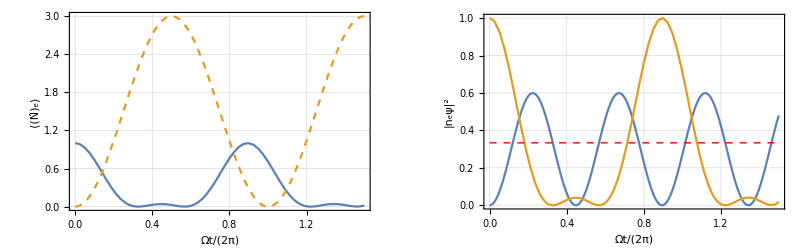

```mathematica
n=3;
k=3;
tsb=Range[0,1.5,0.001];
ψ0=Sum[UnitVector[Length@Hb,i+1]/√k,{i,k}];
onebars=Abs[(1/√3){0,1,1,1,0,0,0,0}.#]^2&/@psisb;
psisb=U[#,Hb].ψ0&/@tsb;
gsb=Transpose@{ts,Abs[UnitVector[Length@Hb,1].#]^2&/@psisb};
onesb=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};
p2=GraphicsRow[
{
Show[
ListLinePlot[
{Transpose@{tsb,Total@{onesb[[All,2]]}}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
],
Plot[{,n Sin[π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
Show[
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
Graphics[{Red,Dashed,Thick,Line[{{0,1/n},{tsb[[-1]],1/n}}]}]
],
ll
},ImageSize->800]
(*Export["nonwstate_RFE.pdf",p2]*)
```

3/5

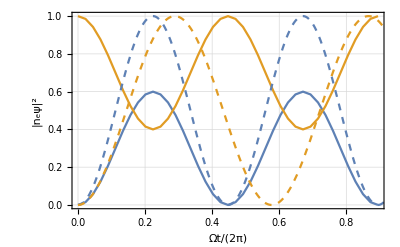

```mathematica
n=5;
k=3;
Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}];
as=Table[couple[n,i],{i,n}]/2;

Hbperf=ArrayFlatten@{
{Δb[[1]],as[[1]]},
{Transpose[as[[1]]],Δb[[2]]}
};
tb=1/√n;
tsb=Range[0,2tb,tb/20];

ψ0=Sum[UnitVector[Length@Hbperf,i+1]/√k,{i,k}];

overlap=Abs[((1/√n)Sum[UnitVector[Length@Hbperf,k+1],{k,n}]).ψ0]^2+Abs[ψ0[[1]]]^2

psisb=U[#,Hbperf].ψ0&/@tsb;
gsb=Transpose@{tsb,Abs[UnitVector[Length@Hbperf,1].#]^2&/@psisb};
onesb=Transpose@{tsb,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};

p2=GraphicsRow[{
Show[
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]],
Plot[{ Sin[√n π t]^2, Sin[√k π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
ll
},ImageSize->800]
```

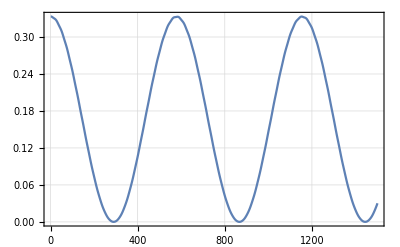

```mathematica
ListLinePlot@onebars
```

{0.380331+0. ⅈ,0.921005+0.084251 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

0.429768

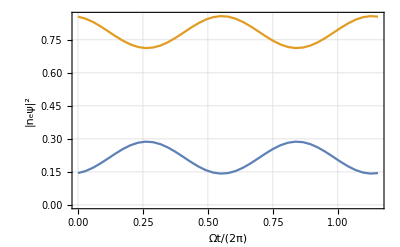

```mathematica
n=3;

Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}];
as=Table[couple[n,i],{i,n}]/2;

Hbperf=ArrayFlatten@{
{Δb[[1]],as[[1]]},
{Transpose[as[[1]]],Δb[[2]]}
};
tb=1/√n;
tsb=Range[0,2tb,tb/20];

ψ0gen[{θ_,ϕ_}]:=Sin[θ]UnitVector[Length@Hbperf,1]+Cos[θ]Exp[ⅈ ϕ]UnitVector[Length@Hbperf,2];
ψ0=ψ0gen[RandomReal[{0,2π},2]]

overlap=Abs[((1/√n)Sum[UnitVector[Length@Hbperf,k+1],{k,n}]).ψ0]^2+Abs[ψ0[[1]]]^2

psisb=U[#,Hbperf].ψ0&/@tsb;
gsb=Transpose@{tsb,Abs[UnitVector[Length@Hbperf,1].#]^2&/@psisb};
onesb=Transpose@{tsb,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};

p2=GraphicsRow[{
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
ll
},ImageSize->800]
```

#### Full Seperable State limits

```mathematica
ndata={};
nlist={2,3,5,8,10};
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
data={};

For[l=1,l≤100000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{π 0.9,1.1π},{n,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
Print[n];
AppendTo[ndata,{n,data}];
]
```

2

3

5

8

10

```mathematica
ndataold=ndata;
```

```mathematica
GraphicsColumn[(ListPlot[#[[All,2]],PlotRange->{{0,1},{0,1}},PlotLabel->"n="<>ToString[#[[1,1]]],ImageSize->Full]&/@Transpose@{ndataold,ndata}),ImageSize->400]
```

-Graphics-

#### Partially separable state limits

```mathematica
ndata={};
nlist=Range[4,8];
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
kdata={};
For[kk=3,kk≤3,kk+=1,
data={};
(*number separable subspaces*)
subspaces=Ceiling[n/kk];
ks=ConstantArray[kk,subspaces];
(*make sure sum of ks equals n*)
ks[[-1]]=n-(subspaces-1)*kk;

For[l=1,l≤50000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{0,2π},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
√ks[[j]] spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
For[l=1,l≤50000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{3π/4,5π/4},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
√ks[[j]] spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
(*Print["k: ",kk];*)
AppendTo[kdata,{kk,data}];
]
Print[n];
AppendTo[ndata,{n,kdata}];
]
```

4

5

6

7

8

```mathematica
$PlotTheme="Detailed";
```

```mathematica
plot=GraphicsGrid@Table[(
Show[
ListPlot[ndata[[k,2,#,2]],ImageSize->250,PlotRange->{{0,1},{0,1}},FrameLabel->{"P0","P1"},PlotLabel->"n="<>ToString[ndata[[k,1]]]<>", k="<>ToString[ndata[[k,2,#,1]]]],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/ndata[[k,1]],{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]&/@Range[Length@ndata[[k,2]]]),
{k,Length@ndata}
];
```

```mathematica
Style[plot,Antialiasing->False]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Reichel_numerical_kpartite.png",plot]
```

Reichel_numerical_kpartite.png

```mathematica
ClearAll[lines];
```

```mathematica
binnum=200;
f[l__]:=Floor[l[[1]],1/binnum]
g[x__]:={N@Floor[x[[1,1]],1/binnum],Max[x[[All,2]]]}
For[m=1,m≤Length@ndata,m+=1,
nn=nlist[[m]];
For[k=3,k<4,k+=1,
(*Print[{nn,k}];*)
ll=GatherBy[ndata[[m,2,1,2]],f];
lines[nn][k]=Interpolation[Sort[g/@ll,#1[[1]]<#2[[1]]&]];
];
]
```

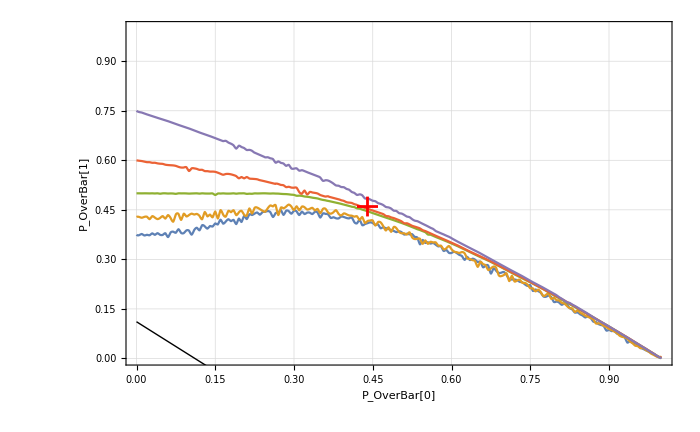

```mathematica
Show[
Plot[Evaluate@Table[lines[m][3][x],{m,8,4,-1}],{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P_OverBar[0]","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18]],
point,
Plot[-x+1/9,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Reichel_k=3_thresholds.pdf",%%]
```

/home/ebert/Dropbox/thesis/introduction/figures

Reichel_k=3_thresholds.pdf

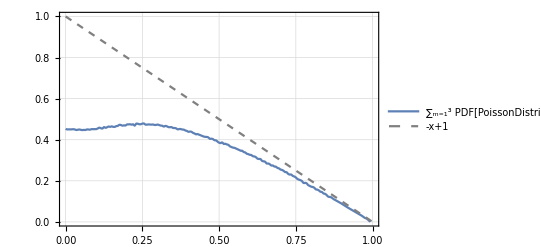

```mathematica
Show[
Plot[Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,3}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][3][x],{m,16,4,-1}],{x,0,1},PlotRange->{0,1}],
Plot[-x+1,{x,0,1},PlotStyle->{Gray,Dashed},PlotRange->{0,1}]
]
```

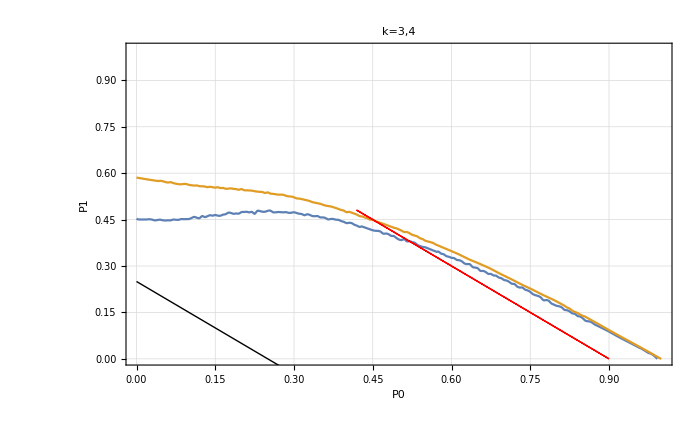

```mathematica
Show[
Plot[Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,3}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][3][x],{m,16,4,-1}],{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P0","P1"},PlotLabel->"k=3,4"],
Plot[{,Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,4}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][4][x],{m,16,5,-1}]},{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P0","P1"},PlotLabel->"k=4"],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/4,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
$PlotTheme="Detailed";
```

```mathematica
Needs["ErrorBarPlots`"]
```

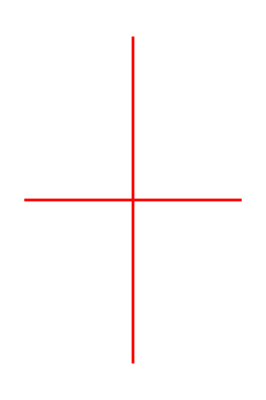

```mathematica
point=Graphics[{
Red,AbsoluteThickness[2],
Line[{{0.42,0.46},{0.46,0.46}}],
Line[{{0.44,0.43},{0.44,0.49}}]
}]
```

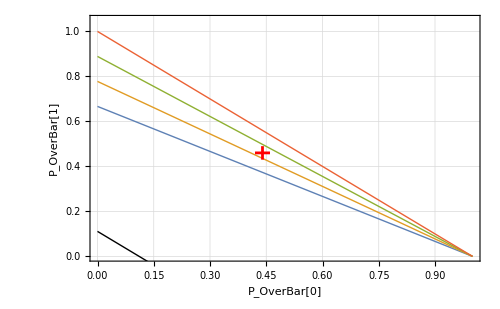

```mathematica
pnew=Show[
Plot[Evaluate@Table[k/9(1-p00),{k,6,9,1}],{p00,0,1},PlotRange->{0,1.05},PlotLegends->None(*{"k=2","k=4","k=6"}*),PlotStyle->AbsoluteThickness[1],FrameLabel->{"P_OverBar[0]","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18],ImageSize->500],
(*ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],*)
point,
Plot[-x+1/9,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
0.48/0.58
```

0.827586

```mathematica
Show[
Plot[Evaluate@Table[k/7(1-p00),{k,3,7,2}],{p00,0,1},PlotRange->{0,1.1},PlotLegends->None(*{"k=2","k=4","k=6"}*),PlotStyle->Dashed,FrameLabel->{"P_0","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18],ImageSize->500],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/4,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["PerfectBlockadeThresholds.pdf",pnew]
```

/home/ebert/Dropbox/thesis/introduction/figures

PerfectBlockadeThresholds.pdf

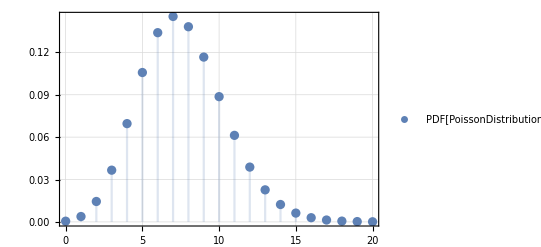

```mathematica
DiscretePlot[PDF[PoissonDistribution[7.6],m],{m,0,20}]
```

```mathematica
f/@{{0.1,1},{0.021,1},{0.001,2},{0.02,3}}
```

{1/10,1/50,0,1/50}

```mathematica
GatherBy[{{0.1,1},{0.021,1},{0.001,2},{0.02,3}},f]
```

{{{0.1,1}},{{0.021,1},{0.02,3}},{{0.001,2}}}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Reichel_numerical_kpartite_n=8_6_4_k=n-1.pdf",plot2]
```

Reichel_numerical_kpartite_n=8_6_4_k=n-1.pdf

#### partially separable states

```mathematica
ndata={};
nlist=Range[3,8];
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
kdata={};
For[kk=2,kk<n,kk+=1,
data={};
(*number separable subspaces*)
subspaces=Ceiling[n/kk];
ks=ConstantArray[kk,subspaces];
(*make sure sum of ks equals n*)
ks[[-1]]=n-(subspaces-1)*kk;

For[l=1,l≤10000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{0,2π},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(*(1/n)*)
Sum[Abs[(*√ks[[j]]*)spinStates[[j,2]]]^2*
Product[Abs[spinStates[[k,1]]]^2,{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
];
AppendTo[data,{p0,p1}];
]
For[l=1,l≤10000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{π/2,3π/2},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(*(1/n)*)
Sum[Abs[(*√ks[[j]]*)spinStates[[j,2]]]^2*
Product[Abs[spinStates[[k,1]]]^2,{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
];
AppendTo[data,{p0,p1}];
]
(*Print["k: ",kk];*)
AppendTo[kdata,{kk,data}];
]
Print[n];
AppendTo[ndata,{n,kdata}];
]
```

3

4

5

6

7

8

```mathematica
plot=GraphicsGrid@Table[(
Show[
ListPlot[ndata[[k,2,#,2]],ImageSize->250,PlotRange->{{0,1},{0,1}},FrameLabel->{"P0","P1"},PlotLabel->"n="<>ToString[ndata[[k,1]]]<>", k="<>ToString[ndata[[k,2,#,1]]]],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2+0.1},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}]
]&/@Range[Length@ndata[[k,2]]]),
{k,Length@ndata}
];
```

```mathematica
Style[plot,Antialiasing->False]
```

-Graphics-

#### Square Root Speed up

```mathematica
f[n_,kbar_,t_]:=Sum[PDF[PoissonDistribution[n],j] Sin[√(j-kbar)π t]^2,{j,kbar,30}]+Sum[PDF[PoissonDistribution[n],j] Sin[π t]^2,{j,kbar}]
```

```mathematica
normal[t_]:=f[7.6,0,t]
singleatom[t_]:=f[7.6,30,t]
kbar1[t_]:=f[7.6,1,t]
Plot[{normal[t],kbar1[t],singleatom[t]},{t,0,0.5},PlotRange->{0,1.05}]
```

-Graphics-

Lets do the fits we would expect

```mathematica
kbar1fit={#,NonlinearModelFit[Table[{t,f[#,1,t]},{t,0,0.5,0.04}],a f[nb,0,t],{{a,1},{nb,#}},t]}&/@Range[3,16];
kbar2fit={#,NonlinearModelFit[Table[{t,f[#,2,t]},{t,0,0.5,0.04}],a f[nb,0,t],{{a,1},{nb,#}},t]}&/@Range[3,16];
```

```mathematica
Plot[Evaluate@(#[[2]][t]&/@kbar1fit),{t,0,0.5},PlotLegends->None]
```

-Graphics-

-1.07665+1.00733 x

-2.06741+1.00783 x

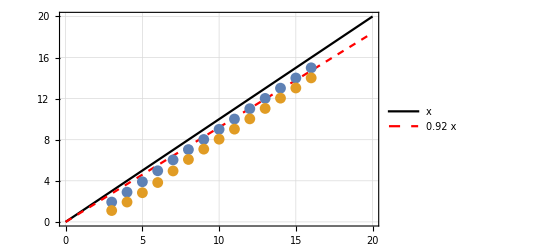

```mathematica
kbar1data={#[[1]],nb/.#[[2]]["BestFitParameters"]}&/@kbar1fit;
Fit[kbar1data,{1,x},x]
kbar2data={#[[1]],nb/.#[[2]]["BestFitParameters"]}&/@kbar2fit;
Fit[kbar2data,{1,x},x]
Show[
Plot[{x,0.92x},{x,0,20},PlotStyle->{Directive[Thick,Black],Directive[Thick,Red,Dashed]}],
ListPlot[{kbar1data,kbar2data},PlotRange->{{0,20},{0,20}}]
]
```

#### maths

```mathematica
state=Flatten@TensorProduct[Delete[Table[{a[i],b[i]},{i,3}],0]];

stateW=Sum[state/.Flatten@Table[If[j==i,{a[i]->0,b[i]->1},{a[i]->1,b[i]->0}],{i,3}],
{j,3}]

P0=TensorProduct[Transpose[{state}],{state}]/.Flatten@Table[{a[i]->1,b[i]->0},{i,3}]//ArrayFlatten;
P1=Sum[
TensorProduct[Transpose[{state}],{state}]/.Flatten@Table[If[j==i,{a[i]->0,b[i]->1},{a[i]->1,b[i]->0}],{i,3}],
{j,3}]//ArrayFlatten;
MatrixForm@P0
Conjugate[state].P0.state

MatrixForm@P1
Conjugate[state].P1.state

stateW.state
```

{0,1,1,0,1,0,0,0}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

a[1] a[2] a[3] Conjugate[a[1] a[2] a[3]]

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

a[2] a[3] b[1] Conjugate[a[2] a[3] b[1]]+a[1] a[3] b[2] Conjugate[a[1] a[3] b[2]]+a[1] a[2] b[3] Conjugate[a[1] a[2] b[3]]

a[2] a[3] b[1]+a[1] a[3] b[2]+a[1] a[2] b[3]

```mathematica
√0.96
```

0.979796

```mathematica
TensorProduct[IdentityMatrix[2],{{0,1},{1,0}}]//MatrixForm
TensorProduct[{{0,1},{1,0}},IdentityMatrix[2]]//MatrixForm
```

((0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0))

((0 | 0
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0))

```mathematica
TensorProduct[{{1,0},{0,-1}},IdentityMatrix[2]]//MatrixForm
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1))

```mathematica
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
```

```mathematica
sx4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σx],If[i≠2,IdentityMatrix[2],σx],If[i≠3,IdentityMatrix[2],σx],If[i≠4,IdentityMatrix[2],σx]],
{i,4}
],4]];
sy4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σy],If[i≠2,IdentityMatrix[2],σy],If[i≠3,IdentityMatrix[2],σy],If[i≠4,IdentityMatrix[2],σy]],
{i,4}
],4]];
sz4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σz],If[i≠2,IdentityMatrix[2],σz],If[i≠3,IdentityMatrix[2],σz],If[i≠4,IdentityMatrix[2],σz]],
{i,4}
],4]];
MatrixForm/@{sx4,sy4,sz4}

state1=Flatten@(TensorProduct[{1,0},{0,1},{0,1},{0,1}]+TensorProduct[{0,1},{1,0},{0,1},{0,1}]+TensorProduct[{0,1},{0,1},{1,0},{0,1}]+TensorProduct[{0,1},{0,1},{0,1},{1,0}]);
state2=Flatten@(TensorProduct[{1,0},{0,1},{0,1},{0,1}]+TensorProduct[{0,1},{1,0},{0,1},{0,1}]-TensorProduct[{0,1},{0,1},{1,0},{0,1}]-TensorProduct[{0,1},{0,1},{0,1},{1,0}]);

jsq4=(sx4.sx4+sy4.sy4+sz4.sz4)/4;
MatrixForm@jsq4

(jsq4.state1)
state1

(jsq4.state2)
state2
```

{(0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0),(0 | -ⅈ | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0 | -ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | ⅈ | ⅈ | 0),(4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4)}

(6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 3 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6)

{0,0,0,0,0,0,0,6,0,0,0,6,0,6,6,0}

{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}

{0,0,0,0,0,0,0,2,0,0,0,2,0,-2,-2,0}

{0,0,0,0,0,0,0,1,0,0,0,1,0,-1,-1,0}

```mathematica
{e,v}=Eigensystem[jsq4];
e
v//MatrixForm
```

{6,6,6,6,6,2,2,2,2,2,2,2,2,2,0,0}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayFlatten@TensorProduct[Transpose[{state1}],{state1}]//MatrixForm
sx4;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayFlatten@TensorProduct[Transpose[{state2}],{state2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)